```mathematica
(* defination *)
SU3:={"r","g","b"};
SU3B:={"R","G","B"};
Core:={{1/2,1/3,{SU3[[1]]}},{-1/2,1/3,{SU3[[2]]}},{0,-2/3,{SU3[[3]]}}};
CoreB:={{-1/2,-1/3,{SU3B[[1]]}},{1/2,-1/3,{SU3B[[2]]}},{0,2/3,{SU3B[[3]]}}};

(* bases generator *)
IndexRoot[rootdiagram_,I3_,Y_]:=Module[{roots=rootdiagram,x=I3,y=Y},
For[find=1,find≤Length[roots],find++,
If[roots[[find,1]]==x && roots[[find,2]]==y,Return[find]]
];
Return[0];
]

ProductBasis[basiset_,SU3_]:=Module[{bases=basiset,su3=SU3},
set={};
For[term=1,term≤Length[bases],term++,
set=Join[set,{bases[[term]]<>su3}];
];
Return[set];
]

ProductTriplet[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[su=1,su≤Length[SU3],su++,
For[i=1,i≤Length[roots],i++,
I3=roots[[i,1]]+Core[[su,1]];
Y=roots[[i,2]]+Core[[su,2]];
index=IndexRoot[diagram,I3,Y];
Basis=ProductBasis[roots[[i,3]],Core[[su,3,1]]];
If[index==0,
diagram=Join[diagram,{{I3,Y,Basis}}],
diagram[[index,3]]=Join[diagram[[index,3]],Basis];
]]
];
Return[diagram];
]

ProductTripletB[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[sub=1,sub≤Length[SU3B],sub++,
For[j=1,j≤Length[roots],j++,
I3=roots[[j,1]]+CoreB[[sub,1]];
Y=roots[[j,2]]+CoreB[[sub,2]];
index=IndexRoot[diagram,I3,Y];
Basis=ProductBasis[roots[[j,3]],CoreB[[sub,3,1]]];
If[index==0,
diagram=Join[diagram,{{I3,Y,Basis}}],
diagram[[index,3]]=Join[diagram[[index,3]],Basis];
]]
];
Return[diagram];
]

(* wave functions generator *)
OperatorA12[]

(* plot tools *)
RootWeightPlot[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[len=1,len≤Length[roots],len++,
diagram=Join[diagram,{{roots[[len,1]],roots[[len,2]]}}];
];
adjacency=Table[0,{x,Length[diagram]},{y,Length[diagram]}];
For[adj1=1,adj1≤Length[diagram],adj1++,
For[adj2=1,adj2≤Length[diagram],adj2++,
distance=((diagram[[adj1,1]]-diagram[[adj2,1]])^2+(diagram[[adj1,2]]-diagram[[adj2,2]])^2)^(1/2);
If[distance==1 || distance==(5/4)^(1/2),
adjacency[[adj1,adj2]]=1;
]
]];
Print[ListPlot[diagram,PlotStyle->PointSize[Large]]];
Print[AdjacencyGraph[adjacency,GraphLayout->"SpringEmbedding"]];
]
```

OperatorA12[]

{{0,0,{rR,gG,bB}},{-1,0,{gR}},{-1/2,-1,{bR}},{1,0,{rG}},{1/2,-1,{bG}},{1/2,1,{rB}},{-1/2,1,{gB}}}

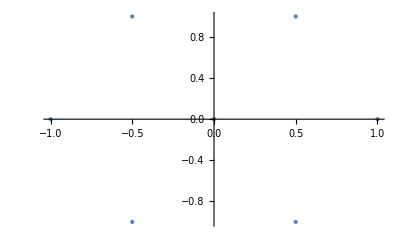

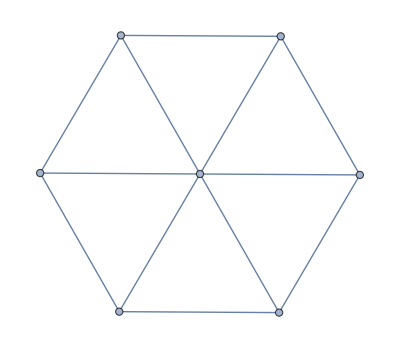

```mathematica
Diagram=ProductTripletB[Core]
RootWeightPlot[Diagram]
```